# Random graphs

## Adding new vertices by using their degree as weight

```mathematica
Get["~/thesis/graphs.m"];
```

## Parameters

```mathematica
startingedges=5;newedges=3;
```

## Functions

```mathematica
addEdgeByDegree[g_]:=Module[{
vertex=VertexCount@g+1,
vs=VertexList@g},
EdgeAdd[VertexAdd[g,vertex],vertex<->#&/@RandomSample[VertexDegree[g,#]+1&/@vs->vs,newedges]]]
```

```mathematica
addEdgeByInvDegree[g_]:=Module[{
vertex=VertexCount@g+1,
vs=VertexList@g},
EdgeAdd[VertexAdd[g,vertex],vertex<->#&/@RandomSample[1./(VertexDegree[g,#]+1)&/@vs->vs,newedges]]]
```

## Play

```mathematica
graph=Graph[Range[startingedges],{}];
```

```mathematica
graph=Nest[addEdgeByDegree,graph,100];//AbsoluteTiming
```

{0.03507,Null}

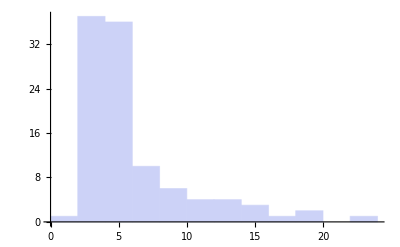

```mathematica
GraphicsRow[{graph,Histogram[VertexDegree[graph,#]&/@VertexList@graph]},ImageSize->Large]
```

```mathematica
{cpl@graph,gcc@graph}
```

{2.68663,0.0852954}

### Inversely proportional to their degree

```mathematica
igraph=Graph[Range[startingedges],{}];
```

```mathematica
igraph=Nest[addEdgeByInvDegree,igraph,100];//AbsoluteTiming
```

{0.04004,Null}

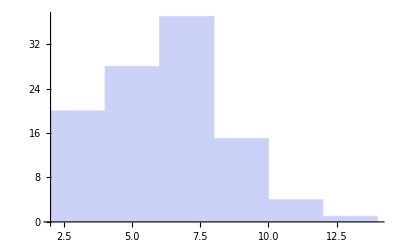

```mathematica
GraphicsRow[{igraph,Histogram[VertexDegree[igraph,#]&/@VertexList@igraph]},ImageSize->Large]
```

```mathematica
{cpl@igraph,gcc@igraph}
```

{2.86319,0.0616314}